```mathematica
Quit
```

```mathematica
clear[Subscript[G, 1],Subscript[G, 2],Subscript[η, 1],Subscript[η, 2],Subscript[η, 3],Subscript[η, 4]]
```

clear[G_1,G_2,η_1,η_2,η_3,η_4]

```mathematica
ClearAll["Global`*"]
```

```mathematica
rns2ni2ns1 = ((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))
```

((-1+G_1) (-1+(1+2 α^2) G_1) η_2^2+(-1+G_2)^2 (1+η_1 (-2-2 α^2+(1+2 α^2) G_1+η_1+(-1+G_1) (-2 α^2+G_1+2 α^2 G_1) η_1)) η_3^2+2 √((-1+G_1) η_2) √(G_1 η_2) √((-1+G_1) (-1+G_2) η_1 η_3) √(G_1 (-1+G_2) η_1 η_3)+(-1+η_4) η_4+G_2^2 (1+(-1+G_1) η_1) (1+(1+2 α^2) (-1+G_1) η_1) η_4^2-2 α^2 √(G_2 η_3) √((-1+G_1) (-1+G_2) η_1 η_3) √((-1+G_2) η_4) √((-1+G_1) G_2 η_1 η_4)-2 √(-((-1+G_2) (-1+η_1) η_3)) √((-1+G_1) (-1+G_2) η_1 η_3) √(-G_2 (-1+η_1) η_4) √((-1+G_1) G_2 η_1 η_4)-2 α^2 √(-((-1+G_2) (-1+η_1) η_3)) √((-1+G_1) (-1+G_2) η_1 η_3) √(-G_2 (-1+η_1) η_4) √((-1+G_1) G_2 η_1 η_4)-2 α^2 √((-1+G_1) η_2) √(G_1 η_2) √((-1+G_1) G_2 η_1 η_4) √(G_1 G_2 η_1 η_4)-2 √((-1+G_1) (-1+G_2) η_1 η_3) √(G_1 (-1+G_2) η_1 η_3) √((-1+G_1) G_2 η_1 η_4) √(G_1 G_2 η_1 η_4)-2 α^2 √((-1+G_1) (-1+G_2) η_1 η_3) √(G_1 (-1+G_2) η_1 η_3) √((-1+G_1) G_2 η_1 η_4) √(G_1 G_2 η_1 η_4)-G_2 (1+(1+α^2) (-1+G_1) η_1) η_4 (-1+2 η_4)-2 (-α^2 √((-1+G_1) η_2) √(G_1 η_2) √((-1+G_1) (-1+G_2) η_1 η_3) √(G_1 (-1+G_2) η_1 η_3)+√(G_2 η_3) √(-((-1+G_2) (-1+η_1) η_3)) √((-1+G_2) η_4) √(-G_2 (-1+η_1) η_4)+√(G_2 η_3) √(G_1 (-1+G_2) η_1 η_3) √((-1+G_2) η_4) √(G_1 G_2 η_1 η_4)+√((-1+G_1) η_2) √(G_1 η_2) √((-1+G_1) G_2 η_1 η_4) √(G_1 G_2 η_1 η_4))+(-1+G_2) η_3 (1+(-1+G_1) η_1 (1+α^2-2 α^2 (-1+G_1) G_2 η_1 η_4))+η_2 (-1+G_1 (1+α^2+2 α^2 (-1+G_1) η_1 ((-1+G_2) η_3-G_2 η_4))))/((-1+(1+α^2) G_1) η_2-η_4+(1+(1+α^2) (-1+G_1) η_1) ((-1+G_2) η_3+G_2 η_4))

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 5.6;
α = 4;

ra1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.101+(2.153×10^-15) G_2-(2.153×10^-15) G_2^2)/(0.088+1.000 G_2)

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 0.8;
Subscript[η, 2] = 0.75;
Subscript[η, 3] = 0.85;
Subscript[η, 4] = 0.92;
Subscript[G, 1] = 5.6;
α = 4;

ra2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.341+0.027 G_2+0.019 G_2^2)/(0.140+1.000 G_2)

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.75;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.85;
Subscript[G, 1] = 5.6;
α = 4;

ra3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.830+0.049 G_2+0.004 G_2^2)/(0.274+1.000 G_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.85;
Subscript[η, 3] = 0.75;
Subscript[η, 4] = 0.9;
Subscript[G, 1] = 5.6;
α = 4;

ra4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.569-0.510 G_2+0.104 G_2^2)/(0.406+1.000 G_2)

```mathematica
Subscript[η, 1] = 0.9;
Subscript[η, 2] = 0.8;
Subscript[η, 3] = 0.7;
Subscript[η, 4] = 0.8;
Subscript[G, 1] = 5.6;
α = 4;

ra5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.521-0.067 G_2+0.064 G_2^2)/(0.230+1.000 G_2)

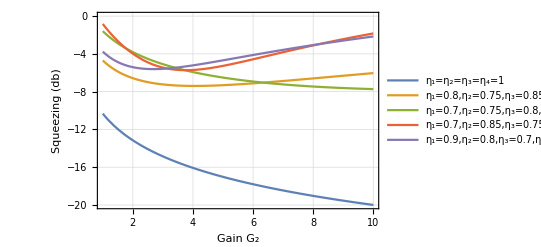

```mathematica
Plot[{10Log10[("0.101"+("2.153"×10^("-15")) Subscript[G, "2"]-("2.153"×10^("-15")) Subscript[G, "2"]^("2"))/("0.088"+"1.000" Subscript[G, "2"])](*1, 1, 1*),10Log10[("0.341"+"0.027" Subscript[G, "2"]+"0.019" Subscript[G, "2"]^("2"))/("0.140"+"1.000" Subscript[G, "2"])](*0.9, 0.9, 0.9*),10Log10[("0.830"+"0.049" Subscript[G, "2"]+"0.004" Subscript[G, "2"]^("2"))/("0.274"+"1.000" Subscript[G, "2"])],10Log10[("1.569"-"0.510" Subscript[G, "2"]+"0.104" Subscript[G, "2"]^("2"))/("0.406"+"1.000" Subscript[G, "2"])],10Log10[("0.521"-"0.067" Subscript[G, "2"]+"0.064" Subscript[G, "2"]^("2"))/("0.230"+"1.000" Subscript[G, "2"])](*0.8, 0.85, 0.7*)},{Subscript[G, 2],1,10},PlotStyle->ScientificForm(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),PlotLegends->{"η_1=η_2=η_3=η_4=1","η_1=0.8,η_2=0.75,η_3=0.85,η_4=0.92","η_1=0.7,η_2=0.75,η_3=0.8,η_4=0.85","η_1=0.7,η_2=0.85,η_3=0.75,η_4=0.9","η_1=0.9,η_2=0.8,η_3=0.7,η_4=0.8"},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["Gain G_2"],HoldForm["R_(ns2 - ni2 - ns1) vs G_2 for G_1 = 5.6, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Quit
```

```mathematica
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rb1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.541-2.765 η_1+1.251 η_1^2)/(0.166+1.000 η_1)

```mathematica
Subscript[η, 2] = 0.75;
Subscript[η, 3] = 0.85;
Subscript[η, 4] = 0.92;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rb2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.008-2.495 η_1+1.812 η_1^2)/(0.141+1.000 η_1)

```mathematica
Subscript[η, 2] = 0.75;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.85;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rb3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.083-2.319 η_1+1.520 η_1^2)/(0.151+1.000 η_1)

```mathematica
Subscript[η, 2] = 0.85;
Subscript[η, 3] = 0.75;
Subscript[η, 4] = 0.9;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rb4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.360-3.558 η_1+2.798 η_1^2)/(0.168+1.000 η_1)

```mathematica
Subscript[η, 2] = 0.8;
Subscript[η, 3] = 0.7;
Subscript[η, 4] = 0.8;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rb5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.339-2.943 η_1+2.036 η_1^2)/(0.174+1.000 η_1)

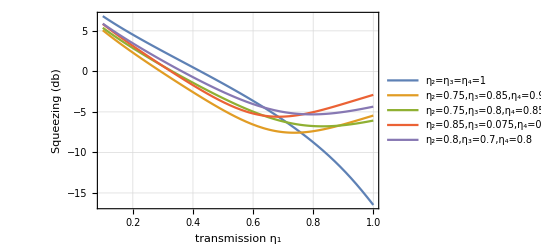

```mathematica
Plot[{10Log10[("1.541"-"2.765" Subscript[η, "1"]+"1.251" Subscript[η, "1"]^("2"))/("0.166"+"1.000" Subscript[η, "1"])](*0.9, 0.9*),10Log10[("1.008"-"2.495" Subscript[η, "1"]+"1.812" Subscript[η, "1"]^("2"))/("0.141"+"1.000" Subscript[η, "1"])](*0.8, 0.7*),10Log10[("1.083"-"2.319" Subscript[η, "1"]+"1.520" Subscript[η, "1"]^("2"))/("0.151"+"1.000" Subscript[η, "1"])],10Log10[("1.360"-"3.558" Subscript[η, "1"]+"2.798" Subscript[η, "1"]^("2"))/("0.168"+"1.000" Subscript[η, "1"])],10Log10[("1.339"-"2.943" Subscript[η, "1"]+"2.036" Subscript[η, "1"]^("2"))/("0.174"+"1.000" Subscript[η, "1"])](*0.8, 0.6*)},{Subscript[η, 1],0.1,1},PlotLegends->{"η_2=η_3=η_4=1","η_2=0.75,η_3=0.85,η_4=0.92","η_2=0.75,η_3=0.8,η_4=0.85","η_2=0.85,η_3=0.075,η_4=0.9","η_2=0.8,η_3=0.7,η_4=0.8"},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_1"],HoldForm["R_(ns2 - ni2 - ns1) vs η_1 for G_1= 5.6, G_2= 4.4, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rc1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(8.243-17.048 η_2+8.975 η_2^2)/(6.547+1.000 η_2)

```mathematica
Subscript[η, 1] = 0.8;
Subscript[η, 3] = 0.85;
Subscript[η, 4] = 0.92;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rc2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(7.733-15.720 η_2+8.975 η_2^2)/(4.672+1.000 η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.85;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rc3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(4.966-11.887 η_2+8.975 η_2^2)/(3.813+1.000 η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.75;
Subscript[η, 4] = 0.9;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rc4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(9.105-16.814 η_2+8.975 η_2^2)/(3.843+1.000 η_2)

```mathematica
Subscript[η, 1] = 0.9;
Subscript[η, 3] = 0.7;
Subscript[η, 4] = 0.8;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rc5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(9.930-17.518 η_2+8.975 η_2^2)/(4.462+1.000 η_2)

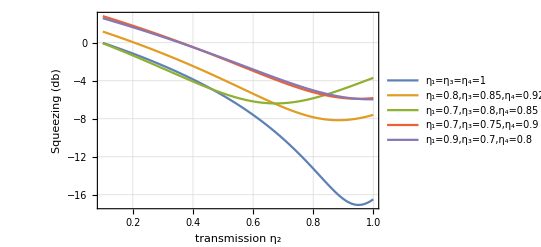

```mathematica
Plot[{10Log10[("8.243"-"17.048" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("6.547"+"1.000" Subscript[η, "2"])](*0.9, 0.9*),10Log10[("7.733"-"15.720" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("4.672"+"1.000" Subscript[η, "2"])](*0.8, 0.7*),10Log10[("4.966"-"11.887" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("3.813"+"1.000" Subscript[η, "2"])],10Log10[("9.105"-"16.814" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("3.843"+"1.000" Subscript[η, "2"])],10Log10[("9.930"-"17.518" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("4.462"+"1.000" Subscript[η, "2"])](*0.8, 0.6*)},{Subscript[η, 2],0.1,1},PlotLegends->{"η_1=η_3=η_4=1","η_1=0.8,η_3=0.85,η_4=0.92","η_1=0.7,η_3=0.8,η_4=0.85","η_1=0.7,η_3=0.75,η_4=0.9","η_1=0.9,η_3=0.7,η_4=0.8"},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_2"],HoldForm["R_(ns2 - ni2 - ns1) vs η_2 for G_1= 5.6, G_2= 4.4, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rd1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(35.935-72.609 η_3+36.734 η_3^2)/(1.640+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.8;
Subscript[η, 2] = 0.75;
Subscript[η, 4] = 0.92;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rd2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(25.869-55.939 η_3+30.604 η_3^2)/(1.513+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.75;
Subscript[η, 4] = 0.85;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rd3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(17.905-43.728 η_3+27.538 η_3^2)/(1.468+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.85;
Subscript[η, 4] = 0.9;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rd4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(19.030-45.166 η_3+27.538 η_3^2)/(1.582+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.9;
Subscript[η, 2] = 0.8;
Subscript[η, 4] = 0.8;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

rd5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(20.278-51.616 η_3+33.670 η_3^2)/(1.343+1.000 η_3)

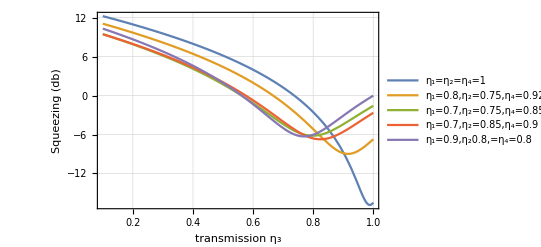

```mathematica
Plot[{10Log10[("35.935"-"72.609" Subscript[η, "3"]+"36.734" Subscript[η, "3"]^("2"))/("1.640"+"1.000" Subscript[η, "3"])](*0.9, 0.9*),10Log10[("25.869"-"55.939" Subscript[η, "3"]+"30.604" Subscript[η, "3"]^("2"))/("1.513"+"1.000" Subscript[η, "3"])](*0.8, 0.7*),10Log10[("17.905"-"43.728" Subscript[η, "3"]+"27.538" Subscript[η, "3"]^("2"))/("1.468"+"1.000" Subscript[η, "3"])],10Log10[("19.030"-"45.166" Subscript[η, "3"]+"27.538" Subscript[η, "3"]^("2"))/("1.582"+"1.000" Subscript[η, "3"])],10Log10[("20.278"-"51.616" Subscript[η, "3"]+"33.670" Subscript[η, "3"]^("2"))/("1.343"+"1.000" Subscript[η, "3"])](*0.8, 0.6*)},{Subscript[η, 3],0.1,1},PlotLegends->{"η_1=η_2=η_4=1","η_1=0.8,η_2=0.75,η_4=0.92","η_1=0.7,η_2=0.75,η_4=0.85","η_1=0.7,η_2=0.85,η_4=0.9","η_1=0.9,η_20.8,=η_4=0.8"},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_3"],HoldForm["R_(ns2 - ni2 - ns1) vs η_3 for G_1= 5.6, G_2= 4.4, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

re1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(48.582-94.207 η_4+45.672 η_4^2)/(1.046+1.000 η_4)

```mathematica
Subscript[η, 1] = 0.8;
Subscript[η, 2] = 0.75;
Subscript[η, 3] = 0.85;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

re2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(30.346-67.403 η_4+37.807 η_4^2)/(0.913+1.000 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.75;
Subscript[η, 3] = 0.8;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

re3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(26.471-59.435 η_4+33.872 η_4^2)/(0.910+1.000 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.85;
Subscript[η, 3] = 0.75;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

re4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(25.990-58.807 η_4+33.872 η_4^2)/(0.910+1.000 η_4)

```mathematica
Subscript[η, 1] = 0.9;
Subscript[η, 2] = 0.8;
Subscript[η, 3] = 0.7;
Subscript[G, 1] = 5.6;
Subscript[G, 2] = 4.4;
α = 4;

re5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) 
√((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-
2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) 
√((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) 
(-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (-α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) 
√((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+
(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2+2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/
((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(24.607-63.526 η_4+41.740 η_4^2)/(0.783+1.000 η_4)

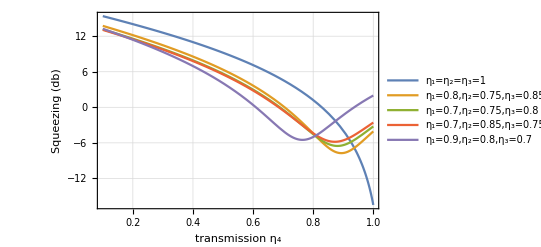

```mathematica
Plot[{10Log10[("48.582"-"94.207" Subscript[η, "4"]+"45.672" Subscript[η, "4"]^("2"))/("1.046"+"1.000" Subscript[η, "4"])](*0.9, 0.9*),10Log10[("30.346"-"67.403" Subscript[η, "4"]+"37.807" Subscript[η, "4"]^("2"))/("0.913"+"1.000" Subscript[η, "4"])](*0.8, 0.7*),10Log10[("26.471"-"59.435" Subscript[η, "4"]+"33.872" Subscript[η, "4"]^("2"))/("0.910"+"1.000" Subscript[η, "4"])],10Log10[("25.990"-"58.807" Subscript[η, "4"]+"33.872" Subscript[η, "4"]^("2"))/("0.910"+"1.000" Subscript[η, "4"])],10Log10[("24.607"-"63.526" Subscript[η, "4"]+"41.740" Subscript[η, "4"]^("2"))/("0.783"+"1.000" Subscript[η, "4"])](*0.8, 0.6*)},{Subscript[η, 4],0.1,1},PlotLegends->{"η_1=η_2=η_3=1","η_1=0.8,η_2=0.75,η_3=0.85","η_1=0.7,η_2=0.75,η_3=0.8","η_1=0.7,η_2=0.85,η_3=0.75","η_1=0.9,η_2=0.8,η_3=0.7",},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_4"],HoldForm["R_(ns2 - ni2 - ns1) vs η_4 for G_1= 5.6, G_2= 4.4, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```